# Regression Visualization

The logistic functions used to simulate regression are created via nonlinear regression through the Desmos API. The goal is to create a function that when a particular component is at that state’s value, we want to return a rate constant’s value for that state. For example, if FC regulates  , and we know FC’s and ’s values across the three states, then we want a function with the following behavior as seen in the plot.

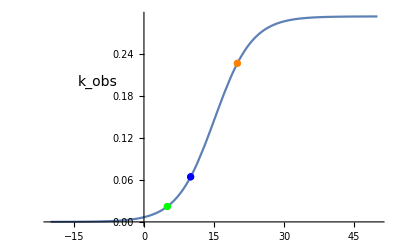
-Graphics-[Sen]

```mathematica
RegFunction[k_, n_, SP_, C_, x_]:=k/(1+Exp[n*(x-SP)])+C
regplot = Plot[RegFunction[0.293708,-0.248768,15.105,0,s],{s,-20,50}];
points = {{20,0.226643},{10,0.0644},{5,0.021998}};
regplots = {regplot, ListPlot[{{points[[1]]},{points[[2]]},{points[[3]]}}, PlotStyle->{Orange, Blue, Green}]};
regressionFigure = Labeled[Show[regplots, Epilog->{Inset[Style[Subscript["k","obs"],FontSize->14,FontFamily->"Source Code Pro"], {-10,0.2}]}, ImageResolution->500], {"[Sen]"},{Bottom}]
```

The three points represent 3 different states -- W (orange), Y (blue), and D (green). Each individual point represents a pair of  (FC , ). We want the line of best fit that goes through each of the points. The solid blue line represents the logistic function found by Desmos through nonlinear regression.